# Cuaderno de Prácticas

## Álgebra

## Grado en Ingeniería Informática

## CURSO 2025/26

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : A
Grupo de prácticas :1

## Práctica 4

```mathematica
(* Cap 5 - 2.2. Matriz de adyacencia - Función 5.1 *)
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1;
matrizadyacencia[[nuevoF[[k,2]],nuevoF[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
(* Cap 5 - 2.2. Matriz de adyacencia - Función 5.2 *)
MATRIZADYACENCIADIR[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1,{k,Length[F]}];
matrizadyacencia];
(* Cap 5 - 4 Grafos Isomorfos - Función 5.10 *)
ISOMORFOS[A1_,A2_]:=Module[{matricesP,i,j},
Isomorfos=False;
If[Dimensions[A1]==Dimensions[A2],   
matricesP=Permutations[IdentityMatrix[Dimensions[A1][[1]]]];   
Do[	      
If[matricesP[[i]].A1.Transpose[matricesP[[i]]]==A2,
Isomorfos=True;matrizP=matricesP[[i]];permutacion=i;Break[];];
   ,{i,Length[matricesP]}];
];

If[Isomorfos,
Print["Son isomorfos, una matriz P es: ",MatrixForm[matrizP], 
      ", una permutación es: ",
MatrixForm[{Table[j,{j,Dimensions[A1][[1]]}],Permutations[Table[j,{j,Dimensions[A1][[1]]}]][[permutacion]]}]]
,Print["No son isomorfos"]];
];
(**)
```

```mathematica
(* Cap 5 - 2.2. Matriz de incidencia - Función 5.5 *)
MATRIZINCIDENCIA[W_,F_]:=Module[{i,j,nuevoF,CONTADORi},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizincidencia=Table[0,{i,Length[W]},{j,Length[F]}];
Do[Do[
matrizincidencia[[nuevoF[[j]][[i]],j]]=1;
,{i,2}];,{j,Length[F]}];
matrizincidencia
];
```

### Ejercicio 5.29 a) Sea W el conjunto formado por todas las cifras distintas que componen su DNI junto con todas las letras distintas de su primer apellido. b) Consideramos el grafo no orientado G₁ cuyo conjunto de vértices es W y donde dos vértices cualesquiera serán adyacentes si y sólo si son: I. Un número par y una vocal. II. Un número impar y una consonante. III. Dos números pares distintos. c) Consideramos el grafo dirigido G₂ cuyo conjunto de vértices es W y donde el conjunto de flechas está formado por todas aquellas flechas que podemos considerar de la forma: I. Origen en un número impar y fin en una vocal. II. Origen en una vocal y fin en una consonante. III. Origen en un número par y fin en un número impar. Se pide:

#### I) Definir G₁ y G₂ directamente por sus conjuntos de vértices y lados o flechas.

```mathematica
W={2,6,8,0,"n","m","a","r","t","i","l","u","s"};
F1={
	{2,"a"},{2,"i"},{2,"u"},{6,"a"},{6,"i"},{6,"u"},{8,"a"},{8,"i"},{8,"u"},
	{0,"n"},{0,"m"},{0,"r"},{0,"t"},{0,"l"},{0,"s"},
	{2,6},{2,8},{6,8}
};
F2={
	{0,"a"},{0,"i"},{0,"u"},
	{"a","n"},{"a","m"},{"a","r"},{"a","t"},{"a","l"},{"a","s"},
	{"i","n"},{"i","m"},{"i","r"},{"i","t"},{"i","l"},{"i","s"},
	{"u","n"},{"u","m"},{"u","r"},{"u","t"},{"u","l"},{"u","s"},
	{2,0},{6,0},{8,0}
};
```

#### II) Calcular las matrices de adyacencia de G₁ y G₂.

```mathematica
A1=MATRIZADYACENCIA[W,F1];
A1//MatrixForm
```

(0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
A2=MATRIZADYACENCIADIR[W,F2];
A2//MatrixForm
```

(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### III) Calcular la matriz de incidencia de G₁.

```mathematica
M1=MATRIZINCIDENCIA[W,F1];
M1//MatrixForm
```

(1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

#### IV) Representar gráficamente G₁ y G₂.

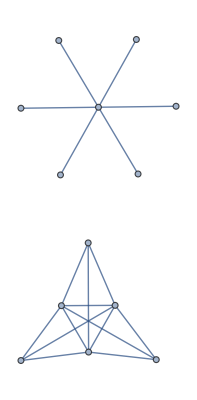

```mathematica
GraphPlot[A1]
```

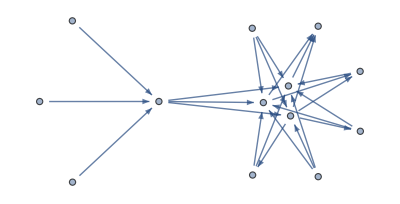

```mathematica
GraphPlot[A2,EdgeRenderingFunction->({Arrow[#1,0.1]}&)]
```

### Ejercicio 2 Calcular conjunto de vértices y lados, matriz de adyacencia, matriz de incidencia y representación gráfica de los grafos del ejercicio 6.8 del manual de prácticas

#### a)

#### b)

#### c)

#### d)

### Ejercicio 3